```mathematica
$Assumptions={Element[{Ω, B, T},Reals]};
Series[(Sin[ω*(t+δ)] - Sin[ω * t])/ω, {δ, 0, 1}]
```

Cos[t ω] δ+O[δ]^2

```mathematica
Integrate[(Sin[ω*a] - Sin[ω * b])*(Sin[ω*c] - Sin[ω * d])/ω^3, {ω, f, ∞}]
```

$Aborted

```mathematica
Integrate[Cos[ω*a] * Cos[ω * b]/ω, {ω, c, ∞}]
```

ConditionalExpression[1/4 (-2 CosIntegral[(a-b) c]-2 CosIntegral[(a+b) c]+2 Log[a-b]-Log[(a-b)^2]+2 Log[a+b]-Log[(a+b)^2]), Re[c]>0&&Im[c]==0]

```mathematica
Integrate[1/(x/a - 1)^3, x]
```

-a/(2 (-1+x/a)^2)

```mathematica
Integrate[1/ω^2 ,{ω, π/T, ∞}]
```

ConditionalExpression[T/π, Im[T]≠0||Sign[T] (1+Sign[T])≠0]

```mathematica
sols = Solve[D[8*Ω*T^2 + 2 * B / (Ω/B - 1) + 2 * π*T, Ω] ==0, Ω]
```

{{Ω→(B (-1+2 T))/(2 T)},{Ω→(B (1+2 T))/(2 T)}}

```mathematica
8*Ω*T^2 + 2 * B / (Ω/B - 1) + 2 * π*T/.Ω->sols[[1]][[1]][[2]]//FullSimplify//Expand
```

-8 B T+2 π T+8 B T^2

```mathematica
8*Ω*T^2 + 2 * B / (Ω/B - 1) + 2 * π*T/.Ω->sols[[2]][[1]][[2]]//FullSimplify//Expand
```

8 B T+2 π T+8 B T^2

```mathematica
8*Ω*T^2 + 2 * B / (Ω/B - 1) + 2 * π*T/.Ω->0
```

-2 B+2 π T

```mathematica
D[D[8*Ω*T^2 + 2 * B / (Ω/B - 1) + 2 * π*T, Ω] , Ω]/.Ω->sols[[2]][[1]][[2]]//FullSimplify//Expand
```

(32 T^3)/B

```mathematica
(Sin[ω * (t + δ)] - Sin[ω*t])//TrigToExp//FullSimplify
```

-Sin[t ω]+Sin[(t+δ) ω]

```mathematica
8*Ω*T^2 + 2 * B / (Ω/B - 1) + 2 * π*T/.Ω->2*B
```

2 B+2 π T+16 B T^2

```mathematica
Series[(Sin[ω*ti])*Sin[ω * tj] - Sin[ω*(ti+δ)]*Sin[ω*(tj)]- Sin[ω*ti]*Sin[ω(tj+δ)]
+Sin[ω*(ti+δ)]*Sin[ω *(tj + δ)], {δ, 0, 3}]
```

ω^2 Cos[ti ω] Cos[tj ω] δ^2+1/2 (-ω^3 Cos[tj ω] Sin[ti ω]-ω^3 Cos[ti ω] Sin[tj ω]) δ^3+O[δ]^4

```mathematica
Integrate[Sin[ω * t]Cos[ω * t]/ω,  {t, 0, T}]
```

ConditionalExpression[Sin[T ω]^2/(2 ω^2), T∈ℝ&&Im[ω]==0&&Re[ω]≠0]

```mathematica
Integrate[1/(2*ω^2)/(ω/(2*B) - 1), {ω, Ω, ∞}]
```

ConditionalExpression[-(2 B+Ω Log[1-(2 B)/Ω])/(4 B Ω), Re[Ω]>0&&Im[Ω]==0]

```mathematica
Log[E]
```

1

```mathematica
formula = 2*Ω*T^2-(2 B+Ω Log[1-(2 B)/Ω])/(4 B Ω) + 2*π*T
```

2 π T+2 T^2 Ω-(2 B+Ω Log[1-(2 B)/Ω])/(4 B Ω)

```mathematica
formula/.Ω->∞
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

```mathematica
sol1 = Solve[D[formula, Ω]==0, Ω][[1]][[1]][[2]];
sol2 = Solve[D[formula, Ω]==0, Ω][[2]][[1]][[2]];
sol3 = Solve[D[formula, Ω]==0, Ω][[3]][[1]][[2]];
```

```mathematica
D[Ω Log[1-(2 B)/Ω], Ω]
```

(2 B)/((1-(2 B)/Ω) Ω)+Log[1-(2 B)/Ω]

1

0.1

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

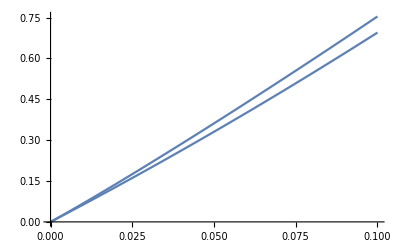

```mathematica
b = 1
bound = .1
Show[Plot[Re[formula/.Ω->sol2/.B->b], {T, 0, bound}], Plot[2*π*T + 20 * b * T^2/3, {T, 0, bound}]]
```

```mathematica
formulasmall = 2*Ω*T^2-1/Ω+2 * π*T
```

2 π T-1/Ω+2 T^2 Ω

```mathematica
Solve[D[formulasmall, Ω]==0, Ω]
```

{{Ω→-ⅈ/(√2 T)},{Ω→ⅈ/(√2 T)}}

```mathematica
formulasmall/.Ω->2B
```

-1/(2 B)+2 π T+4 B T^2

```mathematica
Series[formula/.Ω->sol2, {T, 0, 1}]
```

Power::infy: Infinite expression 1/0^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0 (-1)^(2/3) ComplexInfinity)/((1/B)^(1/3) (B T^4-√(B^2 T^8))^(1/3)) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

```mathematica
sols2
```

sols2

```mathematica
Refine[Re[sol2], {B, T}ϵReals]
```

(2 B)/3+Re[(2 2^(2/3) (1+ⅈ √3) B^2 T^2)/(3 (-27 B T^4-32 B^3 T^6+3 √3 √(27 B^2 T^8+64 B^4 T^10))^(1/3))+((1-ⅈ √3) (-27 B T^4-32 B^3 T^6+3 √3 √(27 B^2 T^8+64 B^4 T^10))^(1/3))/(6 2^(2/3) T^2)]

```mathematica
Refine[Re[B], B∈Reals]
```

B

```mathematica
Re[1]
```

1

```mathematica
1
```

```mathematica
(2* 2^(2/3) *B^2 T^2)/(3 (-27 B T^4-32 B^3 T^6+3 √3 √(27 B^2 T^8+64 B^4 T^10))^(1/3))+((1-ⅈ √3) (-27 B T^4-32 B^3 T^6+3 √3 √(27 B^2 T^8+64 B^4 T^10))^(1/3))/(6 2^(2/3) T^2)
```

```mathematica
Sin[ω*δt*k] - Sin[ω*δt*(k-1)]
```